# Math 223: Homework 6

Ali Heydari

March. 4th, 2021

## Problem 1

The Fresnel sine integral is given by . 
(a) Use integration-by-parts to find the leading behavior of  as and compare your result with what Mathematica computes, which might be slightly different from what you compute. Comment on what you find and which approximation you believe yields a better approximation
overall.

In order to find the asymptotic expansion as , we will perform integration by parts on the integral. We take  and , so now we can write the integration by parts as:
 = 

which gives us the first leading term. Now let us plot this to see what we get:

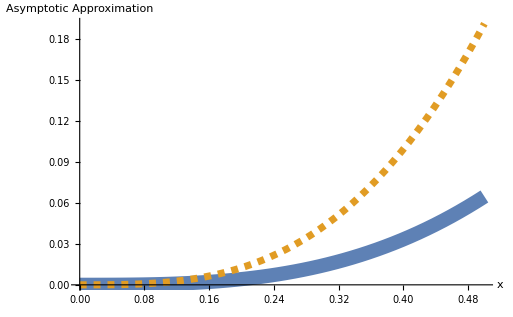

```mathematica
Plot[{FresnelS[x],x*Sin[(Pi*x^2)/2]},{x,0, 0.5},
PlotRange->All,PlotStyle->{Directive[Solid,Thickness[0.02]],Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Asymptotic Approximation", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

Which is pretty terrible. So now to get a more accurate approximation, we can find the next term in the expansion using IBP. That means that we have:

 

 

which results in : 





Now let us compute what Mathematica gives for the asymptotic expansion:

```mathematica
exact = Integrate[Sin[(Pi*t^2)/2],t]
```

FresnelS[t]

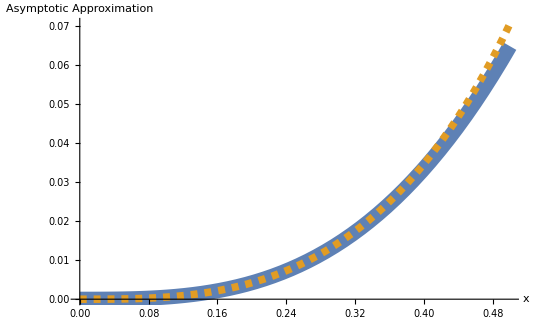

```mathematica
Plot[{FresnelS[x],-(Pi/3)x^3 Cos[(Pi* x^2)/2] +x*Sin[(Pi*x^2)/2]},{x,0, 0.5},
PlotRange->All,PlotStyle->{Directive[Solid,Thickness[0.02]],Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Asymptotic Approximation", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

(b) Use , and integration-by-parts to find the leading behavior of  as . Compare your results with what Mathematica computes, and discuss what you find.

In order to find the asymptotic expansion as x → ∞, we will perform integration by parts on the integral. We could use a u-sub for convenience (as the hint suggests), but If we just think about the chain rule that resulted in the integrand, we can see that there must have been a Cosine term with an coefficient of order 2/(π t) to cancel out the derivative of the sine function. This means that we must take dv = sin((π t^2)/2)  and . Now letting  This will give us:
 , 
And now to make things nicer, we can integrate with respect to (π t^2)/2 instead, which means that   (keep in mind, this trick is just the unmasked version of u-sub).

Now doing the integration by parts yields:

 =  

which gives us the first leading term to be:


 If we want to find more terms of the expansion, we can keep going with the integration by parts. Now to plot this solution against the exact solution:

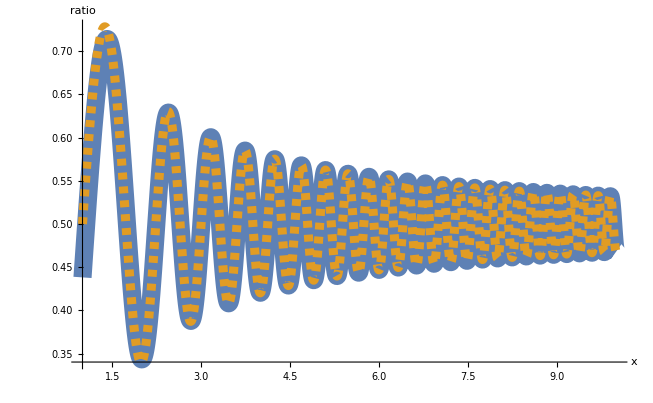

```mathematica
Plot[{FresnelS[x],1/2-(Cos[(Pi*x^2)/2]/(Pi*x)) },{x,1,10},
PlotRange->All,PlotStyle->{Directive[Solid,Thickness[0.02]],Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["ratio", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

this shows that our leading term very well approximates the overall behavior of the Fresnel function, specially as we move further away from 0; this makes sense since our expansion was for x→ ∞. One other observation is that Mathematica’s exact solution behaves rather chaotic as the values of x get larger, but our approximation seems to capture the behavior just as well as smaller values of x. To demonstrate this, let us consider the plot below:

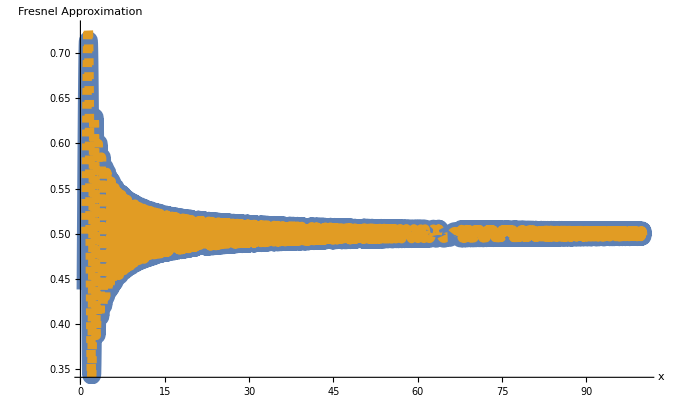

```mathematica
Plot[{FresnelS[x],1/2-(Cos[(Pi*x^2)/2]/(Pi*x)) },{x,1,100},
PlotRange->All,PlotStyle->{Directive[Solid,Thickness[0.02]],Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Fresnel Approximation", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

which shows the chaotic nature of Mathematica’s solution (in blue), while our approximation (in yellow) seems to carry steady on.

## Problem 2

Show that  as  with  being the Euler-Mascheroni constant, defined according to .

We start by making the substitution , which means that , and  . So now we start writing the integral:

Here, we can do the trick where we rewrite 1 as  to the integrand:

Now we can see that we have gotten Euler’s gamma from the second integral, so we can rewrite the solution so far to be: 

Now if we expand the log term using Mathematica

```mathematica
Series[Log[x+1],x-> ∞]
```

Log[x]+O[1/x]^1

So now we can rewrite the asymptotic solution as:

Therefore we have arrived at the desired asymptotic approximation of the integral.